```mathematica
ClearAll["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c U[x]-q U[x]^3+(3/2) q U[x] V[x]-(q/4) U''[x] ,
-c V[x]+(3/4) q V[x]^2-3 q U[x]^2 V[x]+(3 q/4) (U'[x])^2+(3 q/2) U[x] U''[x]-(1/4) q V''[x] 
}/.{U-> Function[x,Subscript[a, 0] +Subscript[a, 1]*P[x]+Subscript[b, 1]*P[x]^(-1)], V-> Function[x,Subscript[c, 0] +Subscript[c, 1]*P[x]+Subscript[c, 2]*P[x]^2+Subscript[d, 1]*P[x]^(-1)+Subscript[d, 2]*P[x]^(-2)]};
```

约束方程：φ'(ξ)=k-(φ(ξ))^2，然后求二次导代入 解的选择来自参考文献
Cakicioglu H, Cinar M, Secer A, et al. On obtaining analytical soliton solutions of Drinfeld-Sokolov-Satsuma-Hirota equation via two efficient methods[J]. Physica Scripta, 2023, 99(1): 015220.
约束3包含整体文件，下面几篇约束均是画图为主

```mathematica
solNice ={{k->-c/q,Subscript[a, 0]->0,Subscript[a, 1]->1,Subscript[b, 1]->0,Subscript[c, 0]->c/q,Subscript[c, 1]->0,Subscript[c, 2]->1,Subscript[d, 1]->0,Subscript[d, 2]->0},{k->-c/q,Subscript[a, 0]->0,Subscript[a, 1]->1/2,Subscript[b, 1]->-c/(2 q),Subscript[c, 0]->c/q,Subscript[c, 1]->0,Subscript[c, 2]->1/2,Subscript[d, 1]->0,Subscript[d, 2]->c^2/(2 q^2)},{k->-c/q,Subscript[a, 0]->0,Subscript[a, 1]->0,Subscript[b, 1]->c/q,Subscript[c, 0]->c/q,Subscript[c, 1]->0,Subscript[c, 2]->0,Subscript[d, 1]->0,Subscript[d, 2]->c^2/q^2}};
solNice//Column
```

{k→-c/q,a_0→0,a_1→1,b_1→0,c_0→c/q,c_1→0,c_2→1,d_1→0,d_2→0}
{k→-c/q,a_0→0,a_1→1/2,b_1→-c/(2 q),c_0→c/q,c_1→0,c_2→1/2,d_1→0,d_2→c^2/(2 q^2)}
{k→-c/q,a_0→0,a_1→0,b_1→c/q,c_0→c/q,c_1→0,c_2→0,d_1→0,d_2→c^2/q^2}

## c>0, q>0 , k<0 ; phi_13

```mathematica
(*(-ρ*√(-k(γ^2-τ^2)-γ √-k Cos[2 √-k(z+Subscript[ξ, 0])]))/(γ*Sin[2 √-k(z+Subscript[ξ, 0])]+τ)*)
(*I*ρ*√-k(1-(2γ)/(γ+Cos[2 √-k(z+Subscript[ξ, 0])]+I*ρ*Sin[2 √-k(z+Subscript[ξ, 0])])) ρ*√k(1-(2γ)/(γ+Cosh[2 √k(z+Subscript[ξ, 0])]+ρ*Sinh[2 √k(z+Subscript[ξ, 0])]));(-ρ √(k(γ^2+τ^2))+γ √k Cosh[2 √k(z+Subscript[ξ, 0])])/(γ*Sinh[2 √k(z+Subscript[ξ, 0])]+τ)*)
(*√k(Tanh[2 √k(z+Subscript[ξ, 0])]-I*ρ*Sech[2 √k(z+Subscript[ξ, 0])])*)
exprk=(-ρ*√(-k(γ^2-τ^2)-γ √-k Cos[2 √-k(z+Subscript[ξ, 0])]))/(γ*Sin[2 √-k(z+Subscript[ξ, 0])]+τ);
(*exprNeg=I*ρ*√-k(1-(2γ)/(γ+Cos[2 √-k(z+Subscript[ξ, 0])]+I*ρ*Sin[2 √-k(z+Subscript[ξ, 0])]));*)
odeolList=P[z]->exprk/.solNice;
```

```mathematica
vNicer= MapThread[(Subscript[c, 0] +Subscript[c, 1]*P[z]+Subscript[c, 2]*P[z]^2+Subscript[d, 1]*P[z]^(-1)+Subscript[d, 2]*P[z]^(-2)/. #1/. #2/. z->(x-c*t))&,{solNice,odeolList}];
uNicer = MapThread[(Subscript[a, 0] +Subscript[a, 1]*P[z]+Subscript[b, 1]*P[z]^(-1)/. #1/. #2/. z->(x-c*t))&,{solNice ,odeolList}];
Grid[Transpose[{k/.solNice,MapIndexed[Subscript[u, First[#2+29]]->#1&,uNicer],MapIndexed[Subscript[v, First[#2+29]]->#1&//TrigToExp,vNicer]}]]
```

-c/q | u_30→-(ρ √((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)]))/(τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)]) | v_30→c/q+(ρ^2 ((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)]))/(τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)])^2
-c/q | u_31→-(ρ √((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)]))/(2 (τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)]))+(c (τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)]))/(2 q ρ √((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)])) | v_31→c/q+(ρ^2 ((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)]))/(2 (τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)])^2)+(c^2 (τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)])^2)/(2 q^2 ρ^2 ((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)]))
-c/q | u_32→-(c (τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)]))/(q ρ √((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)])) | v_32→c/q+(c^2 (τ+γ Sin[2 √(c/q) (-c t+x+ξ_0)])^2)/(q^2 ρ^2 ((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+ξ_0)]))

ρ 要严格正负1  q>0,c>0

-Graphics3D-

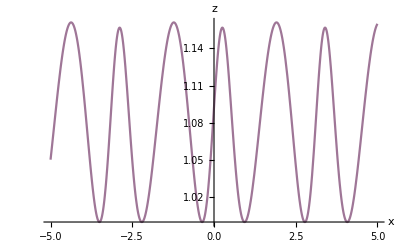

```mathematica
paraC=1;paraQ=1;
paraX0 =1;paraR =-1;
paraT = 4;paraG = 2;
setting1={ClippingStyle->None,
Exclusions->"Singularities"(*{t==x+Log[2]}*)(*"Singularities"*),
ColorFunction-> "TemperatureMap"(*,PlotPoints->60(* 60很顺滑*)*)
};

f[x_,t_]:=-(ρ √((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+Subscript[ξ, 0])]))/(2 (τ+γ Sin[2 √(c/q) (-c t+x+Subscript[ξ, 0])]))+(c (τ+γ Sin[2 √(c/q) (-c t+x+Subscript[ξ, 0])]))/(2 q ρ √((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,γ->paraG,ρ->paraR,τ->paraT};
g[x_,t_]:=c/q+(c^2 (τ+γ Sin[2 √(c/q) (-c t+x+Subscript[ξ, 0])])^2)/(q^2 ρ^2 ((c (γ^2-τ^2))/q-√(c/q) γ Cos[2 √(c/q) (-c t+x+Subscript[ξ, 0])]))/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,γ->paraG,ρ->paraR,τ->paraT};
Plot3D[Abs[f[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_20"," "}]
Plot[Abs[f[x,2]],{x,-5,5},AxesLabel->{x,z},ColorFunction-> "TemperatureMap",
Exclusions->"Singularities"]
```

论文图像,参数收集
paraC=1;paraQ=1;
paraX0 =1;paraR =-1;
paraT = 4;paraG = 2;

```mathematica
GraphicsRow[
{
Plot3D[Abs[f[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],PlotRange->All,

AxesLabel->{"x","t","|u_32|"," "}],
Plot3D[Abs[g[x,t]],{x,-5,5},{t,0,3},Evaluate[setting1],PlotRange->All,
AxesLabel->{"x","t","|v_32|"," "}]
},ImageSize->800]
```

-Graphics-

```mathematica
GraphicsRow[
{ContourPlot[Abs[f[x,t]],{x,-5,5},{t,0,3},Mesh->All,PlotRange->All,
ColorFunction->"TemperatureMap"],
ContourPlot[Abs[g[x,t]],{x,-5,5},{t,0,3},Mesh->All,PlotRange->All,
ColorFunction->"TemperatureMap"]},
ImageSize->800]
```

-Graphics-

```mathematica
(*原始偏微分方程*)
Peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};
(*批量验证，虽然笨拙代码，但很快*)
Map[
(Peqns/. 
{u->Function[{x,t},uNicer[[#]]],
v->Function[{x,t},vNicer[[#]]]
}
)/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,γ->paraG,ρ->paraR,τ->paraT}&,{Table[i,{i,Length[uNicer]}]}
]
```

{{{0,0,0}==0,{0,0,0}==0}}

```mathematica
Clear[v,u]
```

```mathematica
Solve[1-(2 γ)/(γ+Cosh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])]+ρ Sinh[2 √(-c/q) (-c t+x+Subscript[ξ, 0])])==0/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,γ->paraG,ρ->paraR,τ->paraT},{x,t},Reals]
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{t→x+Log[2]}}

```mathematica
Solve[1-Tan[√(c/q) (-c t+x+Subscript[ξ, 0])]==0/.{q->paraQ,c->paraC,Subscript[ξ, 0]->paraX0,γ->paraG,ρ->paraR,τ->paraT},x,Reals]
```

{{x→ConditionalExpression[-1+2 t-√2 (2 ArcTan[1-√2]+2 π C[1]), C[1]∈ℤ]},{x→ConditionalExpression[-1+2 t-√2 (2 ArcTan[1+√2]+2 π C[1]), C[1]∈ℤ]}}